```mathematica
Remove["Global`*"]
expη[x_] := (1+(1-η) x)^(1/(1-η))
logη[x_] :=1/(1-η)(x^(1-η)-1)
```

```mathematica
SetOptions[{Plot,LogLogPlot,ListLogPlot, ListPlot, ListLogLogPlot},
Frame-> True,
LabelStyle->{FontFamily->"Arial", FontSize->12},
AspectRatio->1];
SetOptions[ListLogPlot,  Joined->True, FrameLabel->{"x", " "}];
```

```mathematica
ηVal=8/10;
```

```mathematica
F1[ηVal_]:=Module[{pos, xMax, xMin, yMin, yMax, xStar, p1, p2, p3, p4},
pos=0.9;
xMax = 100;
xMin = 0.1;
yMin = 10^-10;
yMax = 10^15;
xStar = 1/(1 - ηVal);
p1 = LogLogPlot[Exp[x],{x,xMin,xMax},PlotStyle->{Blue,PointSize[.02]},PlotRange->{yMin, yMax},   PlotLegends->Placed[{"e^x"}, {0.26, pos}]];
p2= LogLogPlot[expη[x] /. η-> ηVal,{x,xMin,xMax},PlotStyle->{Gray,PointSize[.02]},PlotRange->All,   PlotLegends->Placed[{"exp_η(x)"}, {0.26, pos-0.15}]];
p3 = LogLogPlot[((1-η)x)^(1/(1-η)) /. η-> ηVal,{x,xMin,xMax},PlotStyle->{Red,PointSize[.02]},PlotRange->All,   PlotLegends->Placed[{"((1-η) x)^(1/(1 - η))"}, {0.26, pos-0.3}]];
p4 = ParametricPlot[{Log@xStar,Log@u},{u,yMin,yMax},PlotStyle->{Black, Dashed}];
txt=Graphics[Text[Style["x_*", 12],{Log @ (0.75xStar),Log @ (10yMin)}]];
Show[{p1,p2, p3, p4, txt},
FrameLabel->{"x", "exp_η(x)"}]
]
```

```mathematica
Manipulate[F1[ηVal], {ηVal, 0.5, 1}]
```

```mathematica
SetDirectory["/Users/colmconnaughton/LML/Projects/notes/gamma-compounding-note"];
```

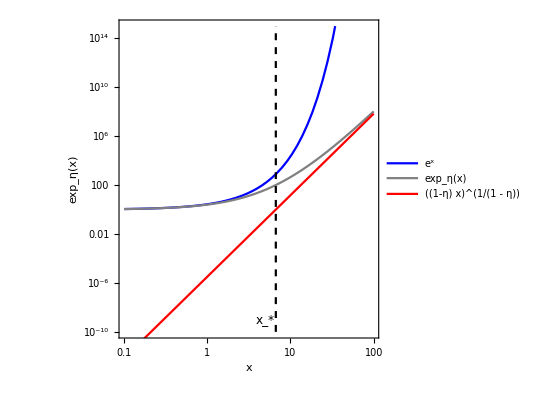

crossover.pdf

```mathematica
p = F1[0.85]
Export["crossover.pdf",p]
```

```mathematica
Limit[((1-η) x)^(1/(1-η)), η-> 1, Direction->"FromBelow"]
```

0

```mathematica
ϕ[x_] := Log[x]-x+1
D[ϕ[x], x]
D[ϕ[x], {x, 2}]
```

-1+1/x

-1/x^2

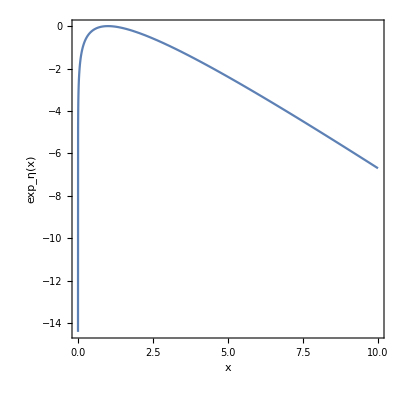

```mathematica
Plot[ϕ[x], {x, 0, 10}]
```

```mathematica
T1= Normal[Series[(1 + s -Exp[s] + τ^2/2), {s, 0, 4}]]
T2 = CoefficientList[T1 /. s-> a0 + τ a1 + a2 τ^2+ a3 τ^3 + a4 τ^4, τ]
```

-s^2/2-s^3/6-s^4/24+τ^2/2

{-a0^2/2-a0^3/6-a0^4/24,-a0 a1-(a0^2 a1)/2-(a0^3 a1)/6,1/2-a1^2/2-(a0 a1^2)/2-(a0^2 a1^2)/4-a0 a2-(a0^2 a2)/2-(a0^3 a2)/6,-a1^3/6-(a0 a1^3)/6-a1 a2-a0 a1 a2-1/2 a0^2 a1 a2-a0 a3-(a0^2 a3)/2-(a0^3 a3)/6,-a1^4/24-(a1^2 a2)/2-1/2 a0 a1^2 a2-a2^2/2-(a0 a2^2)/2-(a0^2 a2^2)/4-a1 a3-a0 a1 a3-1/2 a0^2 a1 a3-a0 a4-(a0^2 a4)/2-(a0^3 a4)/6,-(a1^3 a2)/6-(a1 a2^2)/2-1/2 a0 a1 a2^2-(a1^2 a3)/2-1/2 a0 a1^2 a3-a2 a3-a0 a2 a3-1/2 a0^2 a2 a3-a1 a4-a0 a1 a4-1/2 a0^2 a1 a4,-1/4 a1^2 a2^2-a2^3/6-(a0 a2^3)/6-(a1^3 a3)/6-a1 a2 a3-a0 a1 a2 a3-a3^2/2-(a0 a3^2)/2-(a0^2 a3^2)/4-(a1^2 a4)/2-1/2 a0 a1^2 a4-a2 a4-a0 a2 a4-1/2 a0^2 a2 a4,-(a1 a2^3)/6-1/2 a1^2 a2 a3-(a2^2 a3)/2-1/2 a0 a2^2 a3-(a1 a3^2)/2-1/2 a0 a1 a3^2-(a1^3 a4)/6-a1 a2 a4-a0 a1 a2 a4-a3 a4-a0 a3 a4-1/2 a0^2 a3 a4,-a2^4/24-1/2 a1 a2^2 a3-(a1^2 a3^2)/4-(a2 a3^2)/2-1/2 a0 a2 a3^2-1/2 a1^2 a2 a4-(a2^2 a4)/2-1/2 a0 a2^2 a4-a1 a3 a4-a0 a1 a3 a4-a4^2/2-(a0 a4^2)/2-(a0^2 a4^2)/4,-(a2^3 a3)/6-1/2 a1 a2 a3^2-a3^3/6-(a0 a3^3)/6-1/2 a1 a2^2 a4-1/2 a1^2 a3 a4-a2 a3 a4-a0 a2 a3 a4-(a1 a4^2)/2-1/2 a0 a1 a4^2,-1/4 a2^2 a3^2-(a1 a3^3)/6-(a2^3 a4)/6-a1 a2 a3 a4-(a3^2 a4)/2-1/2 a0 a3^2 a4-(a1^2 a4^2)/4-(a2 a4^2)/2-1/2 a0 a2 a4^2,-(a2 a3^3)/6-1/2 a2^2 a3 a4-1/2 a1 a3^2 a4-1/2 a1 a2 a4^2-(a3 a4^2)/2-1/2 a0 a3 a4^2,-a3^4/24-1/2 a2 a3^2 a4-(a2^2 a4^2)/4-1/2 a1 a3 a4^2-a4^3/6-(a0 a4^3)/6,-(a3^3 a4)/6-1/2 a2 a3 a4^2-(a1 a4^3)/6,-1/4 a3^2 a4^2-(a2 a4^3)/6,-(a3 a4^3)/6,-a4^4/24}

```mathematica
Expand[T, {τ, 0, 4}]
```

1+a0-ⅇ^(a0+a1 τ+s2 τ^2+a3 τ^3+a4 τ^4)+a1 τ-τ^2/2+s2 τ^2+a3 τ^3+a4 τ^4

```mathematica
T2[[{1, 2, 3, 4, 5, 6}]] /. {a0->0, a1->1, a2->-1/6, a3-> 1/36, a4-> 1/216}
```

{0,0,0,0,0,0}

```mathematica
T3 = Normal[Series[1/(Exp[-s]-1), {s, 0, 4}]]
```

-1/2-1/s-s/12+s^3/720

```mathematica
T4 = - τ  /. s -> τ - τ^2/6+τ^3/36 + τ^4/216
```

-τ

```mathematica
Series[T4, {τ, 0, 4}]
```

1+(2 τ)/3+τ^2/12-(5 τ^3)/216-τ^4/720+O[τ]^5

```mathematica
Integrate[x^4 Exp[-t x^2/2], {x, -∞, ∞}, Assumptions->{t>0}]
```

(3 √(2 π))/t^(5/2)

```mathematica
t
```

t

```mathematica
720/3
```

240